```mathematica
files=FileNames["*.tab"];
datas=Drop[Import[#],1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data=Transpose[{ch1s,ch2s}];
```

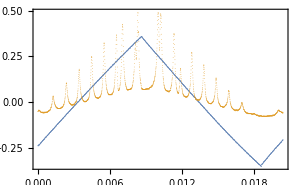
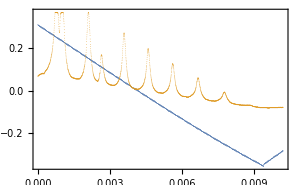
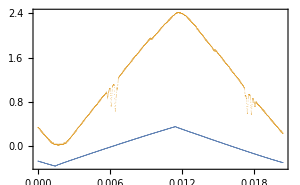
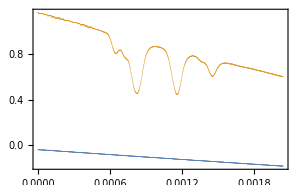
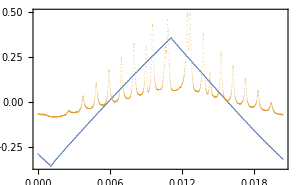
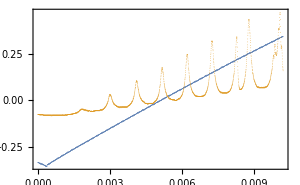
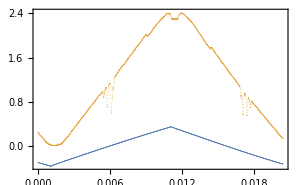
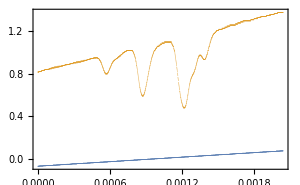

```mathematica
ListPlot[#, PlotRange->All, Frame->True, ImageSize->300, PlotStyle->{PointSize[0.0001]}]&/@ data
```

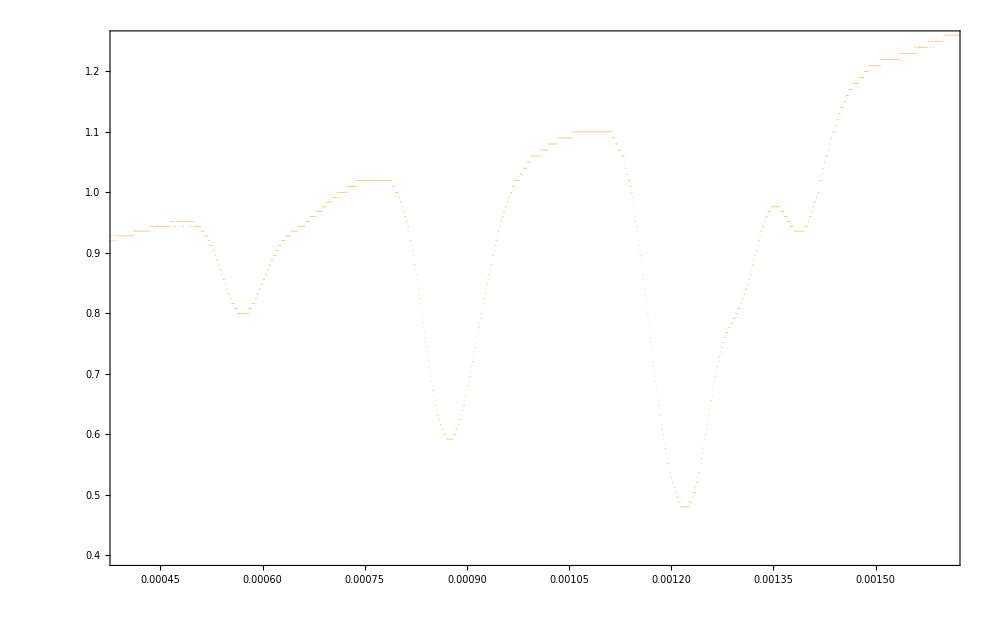

```mathematica
ListPlot[data[[8]], PlotRange->{{0.0004,0.0016}, {0.4, 1.25}}, Frame->True, ImageSize->1000, PlotStyle->{PointSize[0.0001]}]
```

```mathematica
params ={{0.001205,1.098},{0.00128,0.7873},{0.001347,1.105}};
A = Mean[{params[[2, 2]] -params[[1, 2]], params[[2, 2]] - params[[3, 2]] }];
c = params[[2, 1]];
σ = Abs[Mean[{params[[2, 1]] -params[[1, 1]], params[[2, 1]] - params[[3, 1]] }]];
{A, c, σ *10^6}
```

{-0.3142,0.00128,4.}

```mathematica
xminmax ={{0.0008442,0.7374},{0.0009126,0.7345}};
Transpose[xminmax][[1]]
```

{0.0008442,0.0009126}

```mathematica
files
```

{down-etalon.tab,down-etalon_zoom.tab,down-hfs.tab,down-hfs_zoom.tab,up-etalon.tab,up-etalon_zoom.tab,up-hfs.tab,up-hfs_zoom.tab}